```mathematica
Off[General::munfl,FindFit::cvmit,FindFit::sszero,General::stop]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/AcoreNteraction/source_mathematica

```mathematica
(* Johannes fitting parameters *)
LCD={{0.0025, 0.01085409,-1.106057,-1.159333},
{0.0900, 0.01085514,-13.493590, 2.150388},
{0.3025, 0.01085640,-39.797327, 24.965545},
{0.6400, 0.01085554,-80.013554, 81.336340},
{1.1025, 0.01085210,-134.141484, 191.491264},
{1.6900, 0.01085481,-202.185387, 379.175010},
{2.4025, 0.01085130,-284.138103, 683.999621},
{3.2400, 0.01086136,-380.015170, 1143.332900},
{4.2025, 0.01085691,-489.792808, 1884.506079},
{5.2900, 0.01085517,-613.485357, 2977.884003},
{6.5025, 0.01084950,-751.085499, 4589.004608},
{7.8400, 0.01084884,-902.604164, 7067.645881},
{9.3025, 0.01084997,-1068.038344, 10667.304476},
{10.8900, 0.01085217,-1247.387431, 16133.941591},
{12.6025, 0.01085409,-1440.650123, 24382.008195},
{14.4400, 0.01084667,-1647.808037, 36688.658380},
{16.4025, 0.01085322,-1868.905655, 52963.123627},
{18.4900, 0.01087420,-2103.948323, 80952.129573},
{20.7025, 0.01085536,-2352.819143, 119013.695269},
{23.0400, 0.01085344,-2615.638250, 190732.889176}};
```

## Finite differences

```mathematica
SolveSecularNL0[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ]:=Block[{p,Rmax,nGrid,hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,asywf,wf,wffree,Tere,fit,nn,δ,L,r,mod,usol},
p=momentum;
Rmax=Rdis;
nGrid=Npoints;
hDif=Rmax/nGrid;
L=0;

(* Matrix components *)
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{nGrid,nGrid}];
Dmat=DiagonalMatrix[Table[hDif^2 (p^2-mh2 V0[i hDif])+(L(L+1))/i^2,{i,1,nGrid}]];
Wmat=Table[-hDif^3 mh2 W[i hDif,j hDif,mh2^-1 p^2],{i,1,nGrid},{j,1,nGrid}]; 

If[p==0,

bcol=Table[Which[i==nGrid,-hDif,1==1,0],{i,1,nGrid}];
Dmat⟦nGrid⟧⟦nGrid⟧+=1; (*this is only for 0 energy*)

ucol=Array[Subscript["u", ##]&,{nGrid}];
Amat=Dmat+Wmat+Kmat;

usol=LinearSolve[Amat,bcol];
wf=Table[{i hDif,usol⟦i⟧},{i,1,nGrid}];

(*wffree=Table[{i hDif,(usol⟦-1⟧-usol⟦-2⟧) i+usol⟦-2⟧-(usol⟦-1⟧-usol⟦-2⟧) nGrid},{i,1,nGrid}];*)
Tere=Rmax-usol⟦-1⟧;
,

(*Print[" = > 0 energy = "];*)
bcol=ConstantArray[0,nGrid];
ucol=Array[Subscript["u", ##]&,{nGrid}];
Amat=Dmat+Wmat+Kmat;
bcol⟦-1⟧=-1;
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+1;

usol=LinearSolve[Amat,bcol];
wf=Table[{i hDif,usol⟦i⟧},{i,1,nGrid}];

asywf=nn Sin[p r+δ];
fit=FindFit[wf⟦-(IntegerPart[nGrid/10]);;⟧,asywf,{nn,δ},r];
mod=Function[{r},Evaluate[asywf/.fit]];wffree=Table[{i hDif,mod[i hDif]},{i,1,nGrid}];
Tere=(p Cot[δ/.fit⟦2⟧]);
];

{Tere,wffree,wf}
]
```

```mathematica
Scatt1[α0_?NumberQ]:=Block[{f,w},
c0=α0;
f=Replace[w,NDSolve[{w'[r]+w[r]^2-mh2 Vα0[α0,r]==0,w[0]==10^20},w,{r,0,R}]⟦1,1⟧];R-f[R]^-1]
```

## Physics

```mathematica
(***********************)
(*  Physical quantities   *)
   (***********************)
m=1;μ=m/2;hbar=1;mh2=(2 μ)/(hbar)^2;e1=0.1;α=0;
μ=938.92;hbar=197.327053;mh2=(2 μ)/(hbar)^2;
Print["μ = ", μ, " MeV    hbarc = ",hbar, " MeV·fm    h^2/2μ = ", N[1/mh2 ]," MeV·fm^2"];

Λl={0.1,1.,10,100};
```

μ = 938.92 MeV    hbarc = 197.327 MeV·fm    h^2/2μ = 20.7355 MeV·fm^2

```mathematica
μ=938.92;hbar=197.327053;mh2=(2 μ)/(hbar)^2;
Print["μ = ", μ, " MeV    hbarc = ",hbar, " MeV·fm    h^2/2μ = ", N[1/mh2 ]," MeV·fm^2"];
Λl={2.,4.,6.,8.,10.};
```

μ = 938.92 MeV    hbarc = 197.327 MeV·fm    h^2/2μ = 20.7355 MeV·fm^2

```mathematica
Λl=√(4 Transpose[LCD]⟦1⟧);
αl=Transpose[LCD]⟦2⟧;
C0l=Transpose[LCD]⟦3⟧;
D0l=Transpose[LCD]⟦4⟧;
dataC = Transpose[{0.25 Λl^2,C0l}];
C0lslope=Fit[dataC,{1,x},x,"BestFitParameters"];
```

```mathematica
LEC0s={};
αs={};
λs={};
a0s={};

addLs={};
addLls={};

adds={};
addas={};

aleph=1/12.;
Do[{Λ=Λl⟦j⟧;
λ= 0.25 Λ^2;

Λ=Λl⟦j⟧;
α=αl⟦j⟧;
C0=C0l⟦j⟧;
D0=D0l⟦j⟧;

R=30;
(*aleph=Scatt1[C0]^-1;
α=1.5 5  aleph^2;*)
AppendTo[LEC0s,     C0];
AppendTo[αs,     α];
AppendTo[λs,    λ];

nGrid     =1000;
R             =50;
aff=SolveSecularNL0[R,nGrid,0.0]⟦1⟧;
Print["ff: λ = ", λ,,"  C_0: ",C0," - FDM: a_ff = ", aff ];
AppendTo[affs,    aff];



(* Dimer - Dimer non-local*)
nGrid=100;
Rmax=25;
ene=0.;
V0[r_]:=C0 ((2α)/(2α+λ))^(3/2) ⅇ^(-(2α λ)/(2α+λ)r^2);
W[r_,rp_,e_]:=(4π r rp) ( 8 α^(3/2)(mh2^-1(4 α^2 r^2-2 α)+e)ⅇ^(-α(rp^2+r^2))-C0(32 √2 α^3)/(2α+λ)^(3/2)ⅇ^(-α(rp^2+(2α+3λ)/(2α+λ)r^2)));


(*************************)



(*I do the real calculation of dd:*)
add=SolveSecularNL0[Rmax,nGrid,0.0]⟦1⟧;
Print["dd: λ = ", λ," α = ",α," - FDM: (non-local) a_DD = ", add ];
AppendTo[adds,    add];



(* AB - AB non-local, zero-range*)
nGrid=100;

V0[r_]:=C0 ((2α)/λ)^(3/2) ⅇ^(-2α r^2);
W[r_,rp_,e_]:=(4π r rp) ( 8 α^(3/2)(mh2^-1(4 α^2 r^2-2 α)+e)ⅇ^(-α(rp^2+r^2))-C0(32 √2 α^3)/λ^(3/2)ⅇ^(-α(rp^2+3 r^2)));

addL=SolveSecularNL0[R,nGrid,0.0]⟦1⟧;
Print["dd: λ = ", λ," α = ",α," - FDM: (Local) a_DD(0-range) = ", addL ];
AppendTo[addLs,    addL];

(* AB - AB non-local, zero-range, Subscript[c, 0] linear*)
nGrid=100;

V0[r_]:=(C0lslope[[1]]+C0lslope[[2]] λ) ((2α)/λ)^(3/2) ⅇ^(-2α r^2);
W[r_,rp_,e_]:=(4π r rp) ( 8 α^(3/2)(mh2^-1(4 α^2 r^2-2 α)+e)ⅇ^(-α(rp^2+r^2))-(C0lslope[[1]]+C0lslope[[2]] λ)(32 √2 α^3)/λ^(3/2)ⅇ^(-α(rp^2+3 r^2)));

addLl=SolveSecularNL0[R,nGrid,0.0]⟦1⟧;
Print["dd: λ = ", λ," α = ",α," - FDM: (Local) a_DD(0-range,C_0 linear) = ", addLl ];
AppendTo[addLls,    addLl];

(* AB - AB non-local, zero-range, Subscript[c, 0] linear, λ->∞*)
nGrid=100;

V0[r_]:=0;
W[r_,rp_,e_]:=(4π r rp) ( 8 α^(3/2)(mh2^-1(4 α^2 r^2-2 α)+e)ⅇ^(-α(rp^2+r^2)));

addLll=SolveSecularNL0[R,nGrid,0.0]⟦1⟧;
Print["dd: λ = ", λ," α = ",α," - FDM: (Local) a_DD(0-range,C_0 linear, λ→∞) = ", addLll ];
AppendTo[addas,    addLll];



Print[" -- "];
Print[" "];
Print[" "];




},{j,1,Length[Λl]}];
```

ff: λ = 0.0025Null  C_0: -1.10606 - FDM: a_ff = -24.8773

dd: λ = 0.0025 α = 0.0108541 - FDM: (non-local) a_DD = 63.1405

dd: λ = 0.0025 α = 0.0108541 - FDM: (Local) a_DD(0-range) = 11.6512

dd: λ = 0.0025 α = 0.0108541 - FDM: (Local) a_DD(0-range,C_0 linear) = 5.37566

dd: λ = 0.0025 α = 0.0108541 - FDM: (Local) a_DD(0-range,C_0 linear, λ→∞) = 15.7063

--

ff: λ = 0.09Null  C_0: -13.4936 - FDM: a_ff = 15.7067

dd: λ = 0.09 α = 0.0108551 - FDM: (non-local) a_DD = 12.1642

dd: λ = 0.09 α = 0.0108551 - FDM: (Local) a_DD(0-range) = 11.793

dd: λ = 0.09 α = 0.0108551 - FDM: (Local) a_DD(0-range,C_0 linear) = 10.662

dd: λ = 0.09 α = 0.0108551 - FDM: (Local) a_DD(0-range,C_0 linear, λ→∞) = 15.7056

--

ff: λ = 0.3025Null  C_0: -39.7973 - FDM: a_ff = 15.7058

dd: λ = 0.3025 α = 0.0108564 - FDM: (non-local) a_DD = 13.3466

dd: λ = 0.3025 α = 0.0108564 - FDM: (Local) a_DD(0-range) = 13.3868

dd: λ = 0.3025 α = 0.0108564 - FDM: (Local) a_DD(0-range,C_0 linear) = 13.2021

dd: λ = 0.3025 α = 0.0108564 - FDM: (Local) a_DD(0-range,C_0 linear, λ→∞) = 15.7046

--

ff: λ = 0.64Null  C_0: -80.0136 - FDM: a_ff = 15.7064

dd: λ = 0.64 α = 0.0108555 - FDM: (non-local) a_DD = 13.9338

dd: λ = 0.64 α = 0.0108555 - FDM: (Local) a_DD(0-range) = 14.0536

dd: λ = 0.64 α = 0.0108555 - FDM: (Local) a_DD(0-range,C_0 linear) = 14.015

dd: λ = 0.64 α = 0.0108555 - FDM: (Local) a_DD(0-range,C_0 linear, λ→∞) = 15.7053

--

ff: λ = 1.1025Null  C_0: -134.141 - FDM: a_ff = 15.7089

dd: λ = 1.1025 α = 0.0108521 - FDM: (non-local) a_DD = 14.2776

dd: λ = 1.1025 α = 0.0108521 - FDM: (Local) a_DD(0-range) = 14.4247

dd: λ = 1.1025 α = 0.0108521 - FDM: (Local) a_DD(0-range,C_0 linear) = 14.42

dd: λ = 1.1025 α = 0.0108521 - FDM: (Local) a_DD(0-range,C_0 linear, λ→∞) = 15.7078

--

ff: λ = 1.69Null  C_0: -202.185 - FDM: a_ff = 15.7069

dd: λ = 1.69 α = 0.0108548 - FDM: (non-local) a_DD = 14.4977

dd: λ = 1.69 α = 0.0108548 - FDM: (Local) a_DD(0-range) = 14.6569

dd: λ = 1.69 α = 0.0108548 - FDM: (Local) a_DD(0-range,C_0 linear) = 14.6609

dd: λ = 1.69 α = 0.0108548 - FDM: (Local) a_DD(0-range,C_0 linear, λ→∞) = 15.7058

--

ff: λ = 2.4025Null  C_0: -284.138 - FDM: a_ff = 15.7095

dd: λ = 2.4025 α = 0.0108513 - FDM: (non-local) a_DD = 14.6551

dd: λ = 2.4025 α = 0.0108513 - FDM: (Local) a_DD(0-range) = 14.8213

dd: λ = 2.4025 α = 0.0108513 - FDM: (Local) a_DD(0-range,C_0 linear) = 14.8271

dd: λ = 2.4025 α = 0.0108513 - FDM: (Local) a_DD(0-range,C_0 linear, λ→∞) = 15.7083

--

ff: λ = 3.24Null  C_0: -380.015 - FDM: a_ff = 15.7022

dd: λ = 3.24 α = 0.0108614 - FDM: (non-local) a_DD = 14.7633

dd: λ = 3.24 α = 0.0108614 - FDM: (Local) a_DD(0-range) = 14.9327

dd: λ = 3.24 α = 0.0108614 - FDM: (Local) a_DD(0-range,C_0 linear) = 14.9383

dd: λ = 3.24 α = 0.0108614 - FDM: (Local) a_DD(0-range,C_0 linear, λ→∞) = 15.7011

--

ff: λ = 4.2025Null  C_0: -489.793 - FDM: a_ff = 15.7054

dd: λ = 4.2025 α = 0.0108569 - FDM: (non-local) a_DD = 14.854

dd: λ = 4.2025 α = 0.0108569 - FDM: (Local) a_DD(0-range) = 15.0265

dd: λ = 4.2025 α = 0.0108569 - FDM: (Local) a_DD(0-range,C_0 linear) = 15.0313

dd: λ = 4.2025 α = 0.0108569 - FDM: (Local) a_DD(0-range,C_0 linear, λ→∞) = 15.7043

--

ff: λ = 5.29Null  C_0: -613.485 - FDM: a_ff = 15.7067

dd: λ = 5.29 α = 0.0108552 - FDM: (non-local) a_DD = 14.9246

dd: λ = 5.29 α = 0.0108552 - FDM: (Local) a_DD(0-range) = 15.0993

dd: λ = 5.29 α = 0.0108552 - FDM: (Local) a_DD(0-range,C_0 linear) = 15.1031

dd: λ = 5.29 α = 0.0108552 - FDM: (Local) a_DD(0-range,C_0 linear, λ→∞) = 15.7055

--

ff: λ = 6.5025Null  C_0: -751.085 - FDM: a_ff = 15.7108

dd: λ = 6.5025 α = 0.0108495 - FDM: (non-local) a_DD = 14.9846

dd: λ = 6.5025 α = 0.0108495 - FDM: (Local) a_DD(0-range) = 15.1613

dd: λ = 6.5025 α = 0.0108495 - FDM: (Local) a_DD(0-range,C_0 linear) = 15.1642

dd: λ = 6.5025 α = 0.0108495 - FDM: (Local) a_DD(0-range,C_0 linear, λ→∞) = 15.7096

--

ff: λ = 7.84Null  C_0: -902.604 - FDM: a_ff = 15.7113

dd: λ = 7.84 α = 0.0108488 - FDM: (non-local) a_DD = 15.0317

dd: λ = 7.84 α = 0.0108488 - FDM: (Local) a_DD(0-range) = 15.2095

dd: λ = 7.84 α = 0.0108488 - FDM: (Local) a_DD(0-range,C_0 linear) = 15.2117

dd: λ = 7.84 α = 0.0108488 - FDM: (Local) a_DD(0-range,C_0 linear, λ→∞) = 15.7101

--

ff: λ = 9.3025Null  C_0: -1068.04 - FDM: a_ff = 15.7104

dd: λ = 9.3025 α = 0.01085 - FDM: (non-local) a_DD = 15.0702

dd: λ = 9.3025 α = 0.01085 - FDM: (Local) a_DD(0-range) = 15.2489

dd: λ = 9.3025 α = 0.01085 - FDM: (Local) a_DD(0-range,C_0 linear) = 15.2504

dd: λ = 9.3025 α = 0.01085 - FDM: (Local) a_DD(0-range,C_0 linear, λ→∞) = 15.7093

--

ff: λ = 10.89Null  C_0: -1247.39 - FDM: a_ff = 15.7088

dd: λ = 10.89 α = 0.0108522 - FDM: (non-local) a_DD = 15.1022

dd: λ = 10.89 α = 0.0108522 - FDM: (Local) a_DD(0-range) = 15.2814

dd: λ = 10.89 α = 0.0108522 - FDM: (Local) a_DD(0-range,C_0 linear) = 15.2825

dd: λ = 10.89 α = 0.0108522 - FDM: (Local) a_DD(0-range,C_0 linear, λ→∞) = 15.7077

--

ff: λ = 12.6025Null  C_0: -1440.65 - FDM: a_ff = 15.7075

dd: λ = 12.6025 α = 0.0108541 - FDM: (non-local) a_DD = 15.1299

dd: λ = 12.6025 α = 0.0108541 - FDM: (Local) a_DD(0-range) = 15.3095

dd: λ = 12.6025 α = 0.0108541 - FDM: (Local) a_DD(0-range,C_0 linear) = 15.3101

dd: λ = 12.6025 α = 0.0108541 - FDM: (Local) a_DD(0-range,C_0 linear, λ→∞) = 15.7063

--

ff: λ = 14.44Null  C_0: -1647.81 - FDM: a_ff = 15.7128

dd: λ = 14.44 α = 0.0108467 - FDM: (non-local) a_DD = 15.1597

dd: λ = 14.44 α = 0.0108467 - FDM: (Local) a_DD(0-range) = 15.3405

dd: λ = 14.44 α = 0.0108467 - FDM: (Local) a_DD(0-range,C_0 linear) = 15.3408

dd: λ = 14.44 α = 0.0108467 - FDM: (Local) a_DD(0-range,C_0 linear, λ→∞) = 15.7117

--

ff: λ = 16.4025Null  C_0: -1868.91 - FDM: a_ff = 15.7081

dd: λ = 16.4025 α = 0.0108532 - FDM: (non-local) a_DD = 15.1776

dd: λ = 16.4025 α = 0.0108532 - FDM: (Local) a_DD(0-range) = 15.3583

dd: λ = 16.4025 α = 0.0108532 - FDM: (Local) a_DD(0-range,C_0 linear) = 15.3583

dd: λ = 16.4025 α = 0.0108532 - FDM: (Local) a_DD(0-range,C_0 linear, λ→∞) = 15.7069

--

ff: λ = 18.49Null  C_0: -2103.95 - FDM: a_ff = 15.6929

dd: λ = 18.49 α = 0.0108742 - FDM: (non-local) a_DD = 15.184

dd: λ = 18.49 α = 0.0108742 - FDM: (Local) a_DD(0-range) = 15.3631

dd: λ = 18.49 α = 0.0108742 - FDM: (Local) a_DD(0-range,C_0 linear) = 15.3629

dd: λ = 18.49 α = 0.0108742 - FDM: (Local) a_DD(0-range,C_0 linear, λ→∞) = 15.6918

--

ff: λ = 20.7025Null  C_0: -2352.82 - FDM: a_ff = 15.7065

dd: λ = 20.7025 α = 0.0108554 - FDM: (non-local) a_DD = 15.2133

dd: λ = 20.7025 α = 0.0108554 - FDM: (Local) a_DD(0-range) = 15.3945

dd: λ = 20.7025 α = 0.0108554 - FDM: (Local) a_DD(0-range,C_0 linear) = 15.3941

dd: λ = 20.7025 α = 0.0108554 - FDM: (Local) a_DD(0-range,C_0 linear, λ→∞) = 15.7054

--

ff: λ = 23.04Null  C_0: -2615.64 - FDM: a_ff = 15.7079

dd: λ = 23.04 α = 0.0108534 - FDM: (non-local) a_DD = 15.2302

dd: λ = 23.04 α = 0.0108534 - FDM: (Local) a_DD(0-range) = 15.4119

dd: λ = 23.04 α = 0.0108534 - FDM: (Local) a_DD(0-range,C_0 linear) = 15.4112

dd: λ = 23.04 α = 0.0108534 - FDM: (Local) a_DD(0-range,C_0 linear, λ→∞) = 15.7068

--

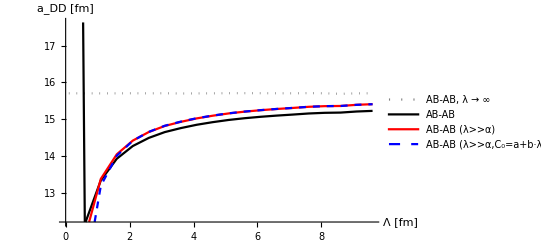

```mathematica
ListLinePlot[{Transpose[{Λl,addas}],Transpose[{Λl,adds}],Transpose[{Λl,addLs}],Transpose[{Λl,addLls}]},AxesLabel->{"Λ [fm]","a_DD [fm]"},PlotStyle->{{Gray,Dotted},{Black},{Red,Opacity->0.2},{Blue,Dashed}},PlotLegends->{"AB-AB, λ → ∞","AB-AB","AB-AB (λ>>α)","AB-AB (λ>>α,C_0=a+b·λ)"}]
```

-9.74877-113.347 x

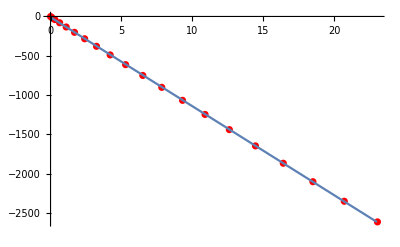

```mathematica
linm=Fit[dataC,{1,x},x]
Show[ListPlot[dataC, PlotStyle->Red], Plot[{linm},{x,0,23}]]
```